```mathematica
tStart=AbsoluteTime[];
```

```mathematica
Clear[Lx,Ly,A,
sx2d,SX2D,sx2dp,SX2DP,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,cx2dp,CX2DP,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
Lx=L;
Ly=L;
A=Lx*Ly;
```

```mathematica
(** m0 = -0.5;**)
```

```mathematica
(**-----------------Define the sine and cosine matrices--------------------**)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2,sx2d[j+1+k Lx,j+k Lx]=I/2},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx2dp[i_Integer,j_Integer]=0;

Do[{sx2dp[(k+1)Lx,1+k Lx]=-I/2,sx2dp[1+k Lx,(k+1)Lx]=I/2},{k,0,Ly-1}]

SX2DP=Table[sx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2,cx2d[j+1+k Lx,j+k Lx]=1/2},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx2dp[i_Integer,j_Integer]=0;

Do[{cx2dp[(1+k)Lx,1+k Lx]=1/2,cx2dp[1+k Lx,(1+k)Lx]=1/2},{k,0,Ly-1}]

CX2DP=Table[cx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianQAHI]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianQAHI[t_,t0_,m_,α_]:=t*(KroneckerProduct[SX2D+α*SX2DP,σ1]+KroneckerProduct[SY2D+α*SY2DP, σ2])+KroneckerProduct[-m*Cons+t0*(CX2D+CY2D+α*CX2DP+α*CY2DP),σ3]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------------Projected Brane--------------------------*)
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

7200

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
(** Comment/Uncomment the rational and irrational equations accordingly **)
```

```mathematica
(**-------Irrational-------**)
```

```mathematica
(** LineUp[x_]:=((1+√5)/2)^-1*(x-1)+8
LineDn[x_]:=((1+√5)/2)^-1*(x-2)+4 **)
```

```mathematica
(**-------Rational-------**)
```

```mathematica
LineUp[x_]:=(2/3)(x-1)+8
LineDn[x_]:=(2/3)*(x-2)+4
```

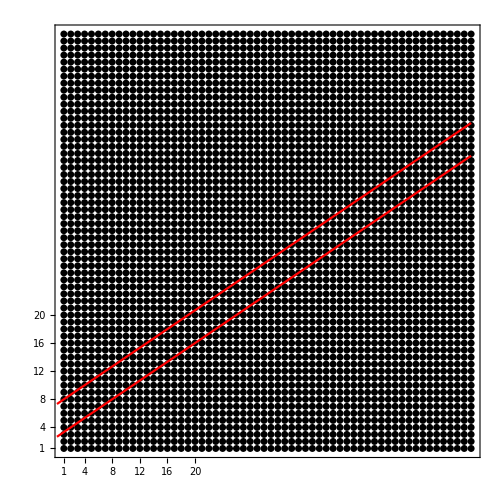

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
(*Plot[2/3*(x-1)+4,{x,0,Lx},PlotStyle-> Blue],Plot[2/3*(x-2)+3,{x,0,Lx},PlotStyle-> Blue],*)
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron]
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
FibonupNew;
```

```mathematica
(** Site indices of the sites in the projected brane **)
```

```mathematica
Fibonlist=Sort[FibonupNew];
```

```mathematica
(** List of Y coordinates of the sites in the projected brane **)
```

```mathematica
YList = Ceiling[Fibonlist/Lx];
```

```mathematica
(** List of X coordinates of the sites in the projected brane **)
```

```mathematica
XList = Fibonlist - (YList - 1)Lx;
```

```mathematica
(** Repeat the coordinates for the two onsite orbitals **)
```

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
(**----Group the orbitals in the sites in Fibonlist ---**)
```

```mathematica
Fibonup = 2 * Fibonlist -1;
```

```mathematica
Fibondown = 2 * Fibonlist;
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
(** This list contains (original) indices of the orbitals within the projected brane **)
```

```mathematica
TotalFibon = Sort[TotalFibon];
```

```mathematica
NOrbitalsBrane=Dimensions[TotalFibon][[1]]
```

520

```mathematica
NOrbitalsBrane/2
```

260

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsBrane
```

6680

```mathematica
(** Percentage of sites within the Brane **)
```

```mathematica
Percentage = N[NOrbitalsBrane/(2*A)]
```

0.0722222

```mathematica
(*-------------F1 is the list of all orbitals in the parent lattice. a is the list of orbitals outside the brane -----------------*)
```

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{7200}

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*----------------------------Create matrices for the Hamiltonian of the projected brane-------------------------------------------*)
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
HTrial=HamiltonianQAHI[1.,1.,m0,0.0];
```

```mathematica
Clear[sx2d,sx2dp,cx2d,cx2dp,sy2d,sy2dp,cy2d,cy2dp,SX2D,SX2DP,CX2D,CX2DP,SY2D,SY2DP,CY2D,CY2DP,Cons,cons]
```

```mathematica
(*---------------This is H11-----------------*)
```

```mathematica
Hfbfb[i_Integer,j_Integer]=0;
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsBrane}
],
{j,1,NOrbitalsBrane}
]
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsBrane},{j,1,NOrbitalsBrane}];
```

```mathematica
(*--------------------This is H22-----------------*)
```

```mathematica
H2d2d[i_Integer,j_Integer]=0;
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
]
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}];
```

```mathematica
(*------------------This is H21------------------*)
```

```mathematica
H2dfb[i_Integer,j_Integer]=0;

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsBrane}
]
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsBrane}];
```

```mathematica
(*------------------This is H12------------------*)
```

```mathematica
Hfb2d[i_Integer,j_Integer]=0;

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsBrane}
],
{j,1,NOrbitalsOutside}
]
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsBrane},{j,1,NOrbitalsOutside}];
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon,OnlyEigenvalue]
```

```mathematica
(** This is the effective Hamiltonian HPTB, defined in Eq. 1 in our paper **)
```

```mathematica
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB);
```

```mathematica
(** To save memory, I delete some matrices which I no longer need **)
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
(**------Check that HFibonRenor is Hermitian------**)
```

```mathematica
(**--- ConjugateTranspose[HFibonRenor] - HFibonRenor//Chop ---**)
```

```mathematica
(** --------------------------------------------------------- **)
```

```mathematica
(**-----------Diagonalize HPTB----------------**)
```

```mathematica
{ValueFibon,VecFibon}=Eigensystem[HFibonRenor];
```

```mathematica
ValVecFibon=SortBy[Transpose[{ValueFibon,VecFibon}],First];
```

```mathematica
ValFibon=Table[{j,ValVecFibon[[j,1]]},{j,1,NOrbitalsBrane}]//Chop;
```

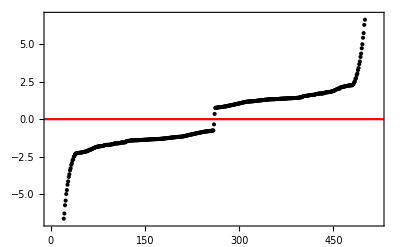

```mathematica
Show[ListPlot[ValFibon,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black(**,PlotRange->{{0,84},{-2,2}}**)],Plot[0,{x,-10,NOrbitalsBrane+10},PlotStyle-> Red]]
```

```mathematica
OnlyEigenvalue=Table[ValFibon[[j,2]],{j,1,NOrbitalsBrane}];
```

```mathematica
Tr[OnlyEigenvalue]//Chop
```

0

```mathematica
(** Real space Chern number calculation as per PHYSICAL REVIEW B 84,241106(R) (2011) **)
```

```mathematica
FilledEigenvectors=Table[ValVecFibon[[i]][[2]], {i,1,NOrbitalsBrane/2}];
```

```mathematica
Clear[P,Q,ChernMatrix,ChernMatrixDiagonalList,ChernMatrixSiteWiseList]
```

```mathematica
(** We create a projector P on the space of filled eigenstates (half-filling limit) **)
```

```mathematica
P = Table[0,{i,1,NOrbitalsBrane},{j,1,NOrbitalsBrane}];
```

```mathematica
Do[P+=TensorProduct[FilledEigenvectors[[i]] ,Conjugate[ FilledEigenvectors[[i]]]],{i, 1, NOrbitalsBrane/2}];
```

```mathematica
Dimensions[P]
```

{520,520}

```mathematica
Q =  IdentityMatrix[NOrbitalsBrane] - P;
```

```mathematica
percentageOfOrbitalsInside = N[NOrbitalsBrane/(2*A)]
```

0.0722222

```mathematica
NSitesInside = NOrbitalsBrane/2
```

260

```mathematica
X1 = DiagonalMatrix[XListKron];
```

```mathematica
Y1 = DiagonalMatrix[YListKron];
```

```mathematica
Max[Abs[P.Q]]
```

6.78944×10^-13

```mathematica
(** Define the local Chern operator **)
```

```mathematica
ChernMatrix=-4π Im[(P.X1.Q.Y1.P)];
```

```mathematica
(** This is the Wanneir orbitalwise list **)
```

```mathematica
ChernMatrixDiagonalList= Diagonal[ChernMatrix];
```

```mathematica
(** Here I take two elements of the list at a time to add the contribution of both onsite orbitals **)
```

```mathematica
ChernMatrixSiteWiseList = Table[ChernMatrixDiagonalList[[2 i]]+ChernMatrixDiagonalList[[2i-1]],{i,1,NOrbitalsBrane/2}];
```

```mathematica
(**------------------------Here I export the list------------------------**)
```

```mathematica
Clear[location,filename1,filename2,filenameString1,filenameString2,filenameString3,filenameString4,filenameString5,filenameString6]
```

```mathematica
location="dataPTB/";
```

```mathematica
filenameString1 = "dataPTBlocalChernAllSitesLx=";
filenameString1a = "dataPTBlocalChernSitesOnLineLx=";
filenameString2="Ly=";
filenameString3 = "m0=";
filenameString4 = "Xup=";
filenameString5 = "Xdn=";
percentageString = "PartsPerThousand=";
```

```mathematica
(** This part checks whether the slope is rational/irrational **)
```

```mathematica
slope = D[LineUp[x],x];
If[Element[slope,Rationals]==True,filenameString6="Rational",filenameString6="Irrational"];
```

```mathematica
(** Finally, we create the filename **)
```

```mathematica
filename1 = StringJoin[location,filenameString1,ToString[Lx],filenameString2,ToString[Ly],filenameString3,ToString[m0],filenameString4,ToString[LineUp[1]],filenameString5,ToString[LineDn[2]],percentageString,ToString[Round[percentageOfOrbitalsInside * 1000]],filenameString6,".dat"]
```

dataPTB/dataPTBlocalChernAllSitesLx=60Ly=60m0=-0.5Xup=8Xdn=4PartsPerThousand=72Rational.dat

```mathematica
filename2 = StringJoin[location,filenameString1a,ToString[Lx],filenameString2,ToString[Ly],filenameString3,ToString[m0],filenameString4,ToString[LineUp[1]],filenameString5,ToString[LineDn[2]],percentageString,ToString[Round[percentageOfOrbitalsInside * 1000]],filenameString6,".dat"]
```

dataPTB/dataPTBlocalChernSitesOnLineLx=60Ly=60m0=-0.5Xup=8Xdn=4PartsPerThousand=72Rational.dat

```mathematica
(** This contains {SiteIndexInOriginalCrystal,Chern(x,y)} **)
```

```mathematica
SiteIndexLocalChern=Table[{XList[[ii]]+(YList[[ii]]-1)*Lx,ChernMatrixSiteWiseList[[ii]]},{ii,1,NOrbitalsBrane/2}];
```

```mathematica
(** This contains {x,y,Chern(x,y)} **)
```

```mathematica
SiteCoordinateLocalChern=Table[{XList[[ii]],YList[[ii]],ChernMatrixSiteWiseList[[ii]]},{ii,1,NOrbitalsBrane/2}];
```

```mathematica
(** Equation of the middle line **)
```

```mathematica
LineMid[x_]:=(LineDn[x]+LineUp[x])/2;
```

```mathematica
(** Sites closest to the middle line **)
```

```mathematica
NearestSiteCoordinateList=Table[{x,Round[LineMid[x]]},{x,1,Lx}]
```

{{1,6},{2,6},{3,7},{4,8},{5,8},{6,9},{7,10},{8,10},{9,11},{10,12},{11,12},{12,13},{13,14},{14,14},{15,15},{16,16},{17,16},{18,17},{19,18},{20,18},{21,19},{22,20},{23,20},{24,21},{25,22},{26,22},{27,23},{28,24},{29,24},{30,25},{31,26},{32,26},{33,27},{34,28},{35,28},{36,29},{37,30},{38,30},{39,31},{40,32},{41,32},{42,33},{43,34},{44,34},{45,35},{46,36},{47,36},{48,37},{49,38},{50,38},{51,39},{52,40},{53,40},{54,41},{55,42},{56,42},{57,43},{58,44},{59,44},{60,45}}

```mathematica
Fibonlist
```

{181,241,242,243,301,302,303,304,361,362,363,364,365,366,422,423,424,425,426,427,483,484,485,486,487,488,489,545,546,547,548,549,550,606,607,608,609,610,611,612,668,669,670,671,672,673,729,730,731,732,733,734,735,791,792,793,794,795,796,852,853,854,855,856,857,858,914,915,916,917,918,919,975,976,977,978,979,980,981,1037,1038,1039,1040,1041,1042,1098,1099,1100,1101,1102,1103,1104,1160,1161,1162,1163,1164,1165,1221,1222,1223,1224,1225,1226,1227,1283,1284,1285,1286,1287,1288,1344,1345,1346,1347,1348,1349,1350,1406,1407,1408,1409,1410,1411,1467,1468,1469,1470,1471,1472,1473,1529,1530,1531,1532,1533,1534,1590,1591,1592,1593,1594,1595,1596,1652,1653,1654,1655,1656,1657,1713,1714,1715,1716,1717,1718,1719,1775,1776,1777,1778,1779,1780,1836,1837,1838,1839,1840,1841,1842,1898,1899,1900,1901,1902,1903,1959,1960,1961,1962,1963,1964,1965,2021,2022,2023,2024,2025,2026,2082,2083,2084,2085,2086,2087,2088,2144,2145,2146,2147,2148,2149,2205,2206,2207,2208,2209,2210,2211,2267,2268,2269,2270,2271,2272,2328,2329,2330,2331,2332,2333,2334,2390,2391,2392,2393,2394,2395,2451,2452,2453,2454,2455,2456,2457,2513,2514,2515,2516,2517,2518,2574,2575,2576,2577,2578,2579,2580,2636,2637,2638,2639,2640,2697,2698,2699,2700,2759,2760,2820}

```mathematica
(** Indices within Fibonlist of the sites in the middle line**)
```

```mathematica
WhichIndicesInFibonlistAreOnTheMiddleLine=Table[Flatten[Position[Fibonlist,NearestSiteCoordinateList[[ii]][[1]] +(NearestSiteCoordinateList[[ii]][[2]]-1)*Lx ]] [[1]],{ii,1,Lx}]
```

{5,6,11,17,18,24,30,31,37,43,44,50,56,57,63,69,70,76,82,83,89,95,96,102,108,109,115,121,122,128,134,135,141,147,148,154,160,161,167,173,174,180,186,187,193,199,200,206,212,213,219,225,226,232,238,239,245,251,252,257}

```mathematica
LineChernList = Table[ChernMatrixSiteWiseList[[WhichIndicesInFibonlistAreOnTheMiddleLine[[ii]]]],{ii,1,Lx}]
```

{14.2049,2.75043,-0.0586171,-0.718921,-0.885987,-0.919435,-0.931485,-0.934108,-0.931654,-0.934901,-0.934953,-0.931899,-0.934966,-0.934967,-0.931901,-0.934967,-0.934968,-0.931901,-0.934968,-0.934968,-0.931901,-0.934968,-0.934968,-0.931901,-0.934968,-0.934968,-0.931901,-0.934968,-0.934968,-0.931901,-0.934968,-0.934968,-0.931901,-0.934968,-0.934968,-0.931901,-0.934968,-0.934968,-0.931901,-0.934968,-0.934968,-0.931901,-0.934968,-0.934967,-0.931901,-0.934968,-0.934967,-0.9319,-0.934966,-0.934954,-0.931861,-0.934773,-0.934094,-0.928684,-0.92299,-0.883137,-0.740678,-0.13101,2.47625,11.5884}

```mathematica
LineChernListExport = Table[{NearestSiteCoordinateList[[ii]][[1]],NearestSiteCoordinateList[[ii]][[2]],LineChernList[[ii]]},{ii,1,Lx}]
```

{{1,6,14.2049},{2,6,2.75043},{3,7,-0.0586171},{4,8,-0.718921},{5,8,-0.885987},{6,9,-0.919435},{7,10,-0.931485},{8,10,-0.934108},{9,11,-0.931654},{10,12,-0.934901},{11,12,-0.934953},{12,13,-0.931899},{13,14,-0.934966},{14,14,-0.934967},{15,15,-0.931901},{16,16,-0.934967},{17,16,-0.934968},{18,17,-0.931901},{19,18,-0.934968},{20,18,-0.934968},{21,19,-0.931901},{22,20,-0.934968},{23,20,-0.934968},{24,21,-0.931901},{25,22,-0.934968},{26,22,-0.934968},{27,23,-0.931901},{28,24,-0.934968},{29,24,-0.934968},{30,25,-0.931901},{31,26,-0.934968},{32,26,-0.934968},{33,27,-0.931901},{34,28,-0.934968},{35,28,-0.934968},{36,29,-0.931901},{37,30,-0.934968},{38,30,-0.934968},{39,31,-0.931901},{40,32,-0.934968},{41,32,-0.934968},{42,33,-0.931901},{43,34,-0.934968},{44,34,-0.934967},{45,35,-0.931901},{46,36,-0.934968},{47,36,-0.934967},{48,37,-0.9319},{49,38,-0.934966},{50,38,-0.934954},{51,39,-0.931861},{52,40,-0.934773},{53,40,-0.934094},{54,41,-0.928684},{55,42,-0.92299},{56,42,-0.883137},{57,43,-0.740678},{58,44,-0.13101},{59,44,2.47625},{60,45,11.5884}}

```mathematica
Mean[LineChernList]
```

-0.317686

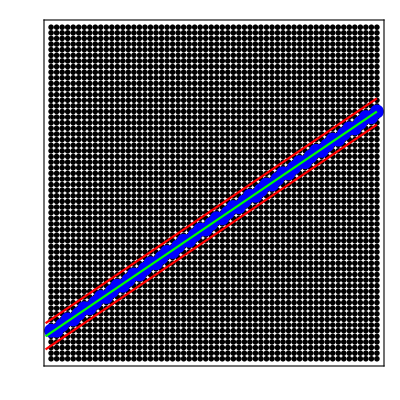

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
ListPlot[NearestSiteCoordinateList,PlotStyle-> {Blue,PointSize[0.025]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineMid[x],{x,0,Lx},PlotStyle-> Green],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 18,
FrameTicks-> None,
ImageSize-> 400,AspectRatio-> 1
]
```

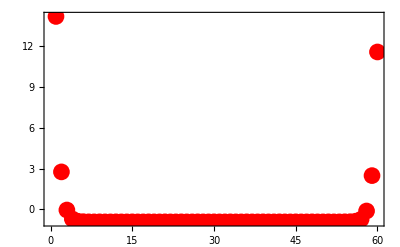

```mathematica
ListPlot[LineChernList,PlotRange->All,Frame->True,PlotStyle-> {Red,PointSize[0.03]},Axes->False]
```

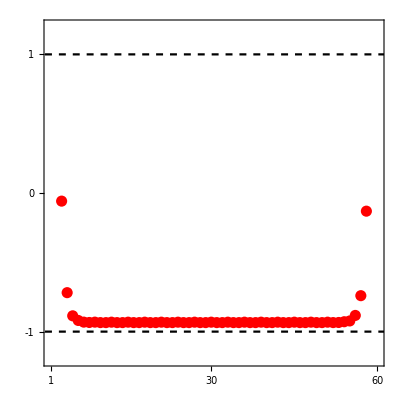

```mathematica
Show[Plot[1,{x,0,Lx+2},PlotStyle->{Dashed,Black},PlotRange->{{1,Lx},{-1.2,1.2}},Frame->True,Axes->False],
Plot[-1,{x,0,Lx+2},PlotStyle->{Dashed,Black},PlotRange->{{1,Lx},{-1.2,1.2}},Frame->True,Axes->False],
ListPlot[LineChernList,PlotRange->{-1.2,1.2},Frame->True,PlotStyle-> {Red,PointSize[0.02]},Axes->False],
(**ListPlot[-LineChernList,PlotRange->{-1.2,1.2},Frame->True,PlotStyle-> {Blue,PointSize[0.02]},Axes->False], **)
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 24,
FrameTicks->{ {{{-1,"-1"},{0,"0"},{1,"1"}},None},{{1,Lx/2,Lx},None}},
ImageSize-> 400,AspectRatio-> 1]
```

```mathematica
(** Here we export the files **)
```

```mathematica
Export[filename1,SiteCoordinateLocalChern];
```

```mathematica
Export[filename2,LineChernListExport];
```

```mathematica
(**----------------------------------------------------------------------------------------**)
```

```mathematica
(**----------------------------------------------------------------------------------------**)
```

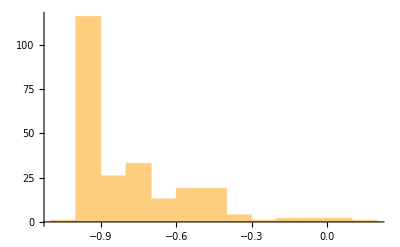

```mathematica
Histogram[ChernMatrixSiteWiseList]
```

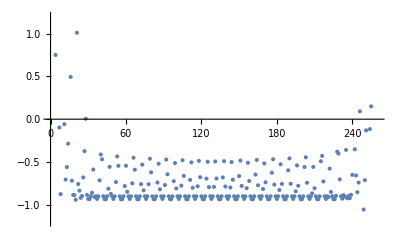

```mathematica
ListPlot[ChernMatrixSiteWiseList,PlotRange->{-1.2,1.2}]
```

```mathematica
Mean[ChernMatrixSiteWiseList]
```

-7.82963×10^-15

```mathematica
tStop=AbsoluteTime[];
```

```mathematica
tStop - tStart
```

627.243913